# Sezione c.

## Cose fatte prima

Creiamo un visualizzatore stupido del punto attrattivo in funzione di μ.

```mathematica
attrattivoPlot[nx_,n_,η_]:=With[{f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{0,4},{0,1}},AspectRatio->Automatic,
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

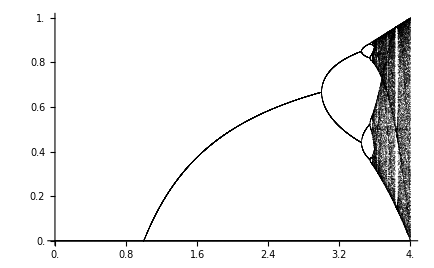

```mathematica
attrattivoPlot[30,10^4,10^4]
```

```mathematica
With[
{
f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)],
n=10^4,
η=10^4,
nx=30
},
Export[
"sas.csv",
Union@Flatten[
Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],
1
]
]
]
```

```mathematica
With[{a=Import["D:\\Università\\Laboratorio computazionale\\Esercizi\\01_Esame\\zzz_zoom_attrattori_contro_mu.csv"]},
ListPlot[a,PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{3.4,4},{0,1}},AspectRatio->Automatic,
Ticks->{Subdivide[3.4,4.,6],Subdivide[0,1.,10]}]]
```

```mathematica
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
```

```mathematica
g[μ_,n_]:=With[{x=Solve[{z==fn[μ,z,n],0<z≤1},z,Reals]⟦1,1,2⟧},D[fn[μ,ξ,n],ξ]/.{ξ:>x}]
```

```mathematica
g[3,2]
```

1

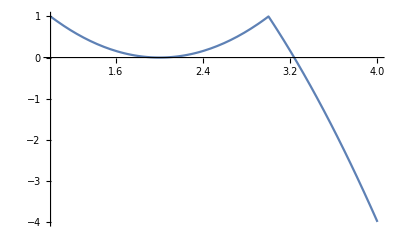

```mathematica
Plot[g[μ,2],{μ,1,4}]
```

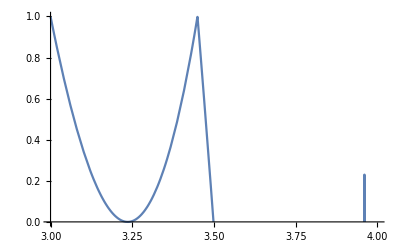

```mathematica
Plot[g[μ,4],{μ,3,4},PlotRange->{0,1}]
```

```mathematica
D[fn[3,x,2],x]/.x->2/3
```

1

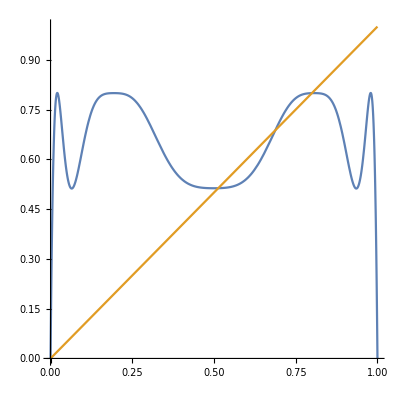

```mathematica
Plot[{fn[3.2,x,4],x},{x,0,1},AspectRatio->Automatic]
```

```mathematica
1.9/2.9
```

0.655172

```mathematica
Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]
```

```mathematica
DeleteCases[Drop[First/@Flatten[Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]/.Rule->List/.{x,y_}->y],1],_Root]
```

{(-1+μ)/μ,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2),(1+μ)/(2 μ)+1/2 √((-3-2 μ+μ^2)/μ^2)}

```mathematica
x[μ_]:=1-1/μ
x4[μ_]:=(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->x4[μ]}]
```

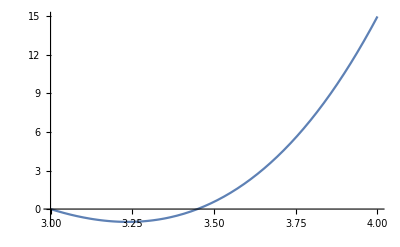

```mathematica
Plot[g[μ,4]-1.,{μ,3,4},PlotRange->Full]
```

```mathematica
Flatten[Solve[g[μ,4]==1,μ,Reals]/.Rule[μ,x_]->x]//Max
```

1+√6

```mathematica
Solve[{fn[μ,x,8]-x==0,μ>1+√6},x,Reals]
```

$Aborted

```mathematica
ClearAll[x]
```

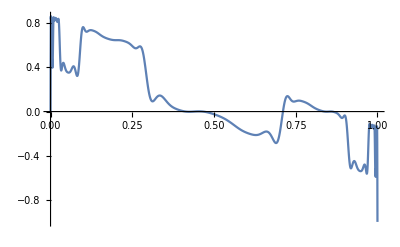

```mathematica
With[{μ=1+√6+10^-2},Plot[{fn[μ,ξ,8]-ξ},{ξ,0,1}]]
```

```mathematica
With[{μ=1+√6+$MachineEpsilon},FindRoot[{fn[μ,ξ,8]-ξ},{ξ,0.5}]]
```

{ξ→0.43996}

```mathematica
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->0.43996001699979026}]
```

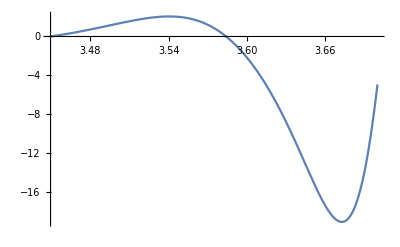

```mathematica
Plot[g[μ,8]-1,{μ,1+√6,3.7}]
```

```mathematica
FindRoot[FunctionInterpolation[g[μ,8]-1,{μ,1+√6,4}][μ],{μ,3.6}]
```

{μ→3.58402}

## Cose fatte poi